# Assignment 1

Course code: IX1500
Date: 20yy-mm-dd

Name 1, name1@kth.se
Name 2, name2@kth.se

Task 1: 3.1

## Summery

### Task

A partical moves in a the xy plane according to the following moves:
U :(m, n) → (m + 1, n + 1) (1)
L :(m, n) → (m + 1, n − 1), (2)
where m, n are integers. For example see the following Figure.

(a) How many such paths are there from (0, 3) to (7, 2). Explain and print all
such paths. For example, the path that corresponds to the above figure is
LLLLUUU.
(b) How many paths from (0, 3) to (7, 2) touch or cross x−axis at least once.
Explain and print all such paths.
(c) How many paths from (0, 3) to (7, 2) never touch or cross x−axis. Explain
and print all such paths.
(d) How many paths from (5, 5) to (30, 10) never touch or cross x−axis. Ex.02plain your solution.

### Result

a) The amount of permutations is 35. 
b)
c)
d)

## Road Construction

### Model for cross section area

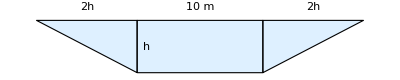

The given trapezoid area is

a(h)=(10+2h)h

x [m] | h [m] | a [m^2]
0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

The data is interpolated as a function A(x).

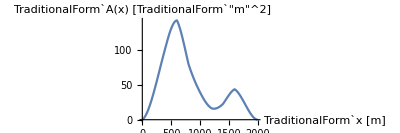

### Model for volume

The requested volume to be transported can be calculated numerically with the integral

V=∫_0^2000 A(x)dx

V≈101×10^3 m^3

I.e. about 0.1 km^3 must be transported.

## Code

```mathematica
ClearAll["`*"]
```

define L, and U movements

```mathematica
l = {1,-1};
u={1,1};
```

using a recursive function, we define the function “coords” that takes a list of L,U movements and converts it to absolute coordinates

```mathematica
f[0,l_] := {0,3}
f[n_, l_] := f[n-1,l] + l[[n]]
coords[l_] := f[#,l] & /@ Range[0,7]
```

we define two plotting functions, one to plot a single permutation, and one to take a full list of different permutations and plotting them all.

```mathematica
plot[l_]:=ListPlot[{coords[l]},{Joined -> True, PlotRange->{-2,6}}]
plotall[l_] := Map[plot, l]
```

#### a)

list all permutations of our moveset and plot them.

```mathematica
a = Permutations[{l,l,l,l,u,u,u}];
graphsa = plotall[a];
Manipulate[graphsa[[x]],{x,1,Length[graphsa],1}]
```

#### b)

list all permutations that touches the x axle and plot them

```mathematica
b1 = Permutations[{l,l,l,l,u}];
b1= Join[#,{u,u}]& /@ b1;
b2 = Permutations[{l,u,u,u}];
b2 = Join[{l,l,l},#]&/@b2;
b = Union[b1,b2];

graphsb = plotall[b];
Manipulate[graphsb[[x]],{x,1,Length[graphsb],1}]
```

#### c)

this is simply all permutations found in a but not in b, c=a\b

```mathematica
c = Complement[a,b];
graphsc = plotall[c];
Manipulate[graphsc[[x]],{x,1,Length[graphsc],1}]
```

Task 2: 3.2 (Den svåra)

## Summery

### Task

The candidates A and B are the finalist for an award. A committee of 14
members will place their vote (in favour of one of the candidates) into a ballot
box. Suppose that A receives 9 votes and B receives 5. In how many ways
the ballot can be selected, one at a time, from the ballot box so that there are
always more votes in favour of A. Explain your solution and print all such ways.

### Result

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

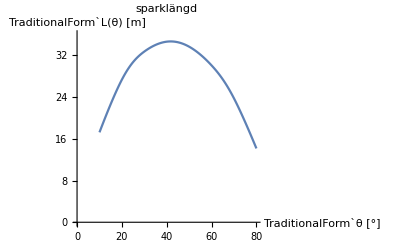

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code